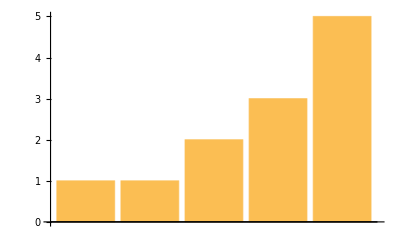

-Graphics-

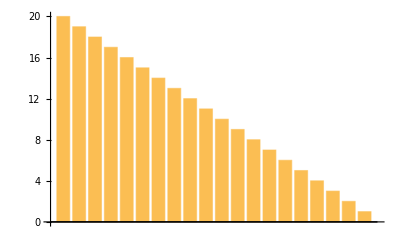

1
2
3
4
5

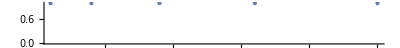

-Graphics-

-Graphics-

{-Graphics-,-Graphics-,-Graphics-}

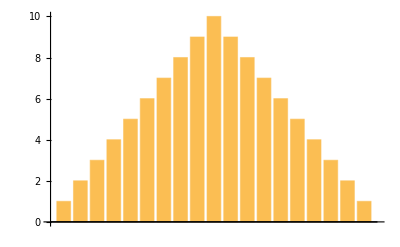

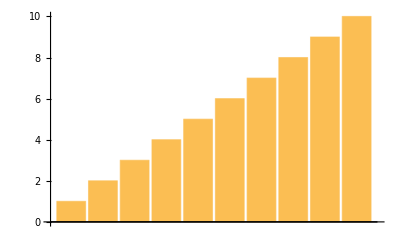
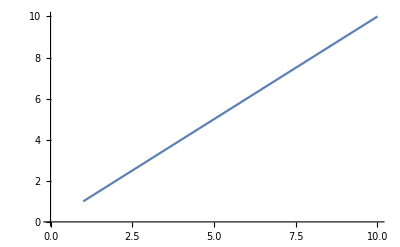
{-Graphics-,-Graphics-,-Graphics-}

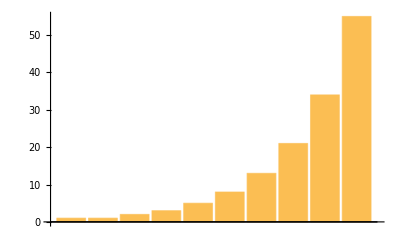
{-Graphics-,-Graphics-}

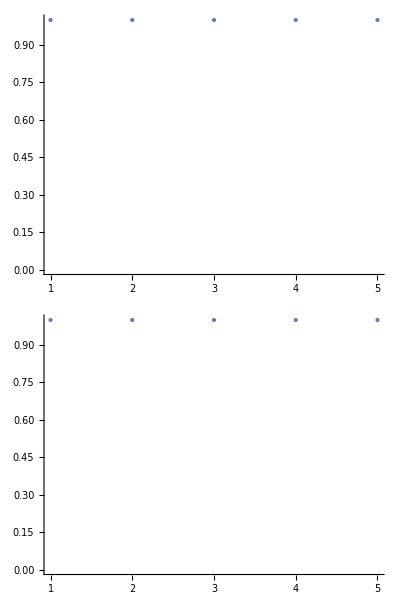

{1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9}

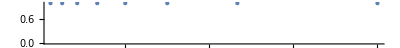

```mathematica
(* 4.1 *)
BarChart[{1, 1, 2, 3, 5}]

(* 4.2 *)
PieChart[Range[10], ImageSize -> Tiny]

(* 4.3 *)
BarChart[Reverse[Range[20]]]

(* 4.4 *)
Column[Range[5]]

(* 4.5 *)
mysquares = Range[5]^2;
NumberLinePlot[mysquares]

(* 4.6 *)
PieChart[ConstantArray[1, 10], ImageSize->Tiny]

(* 4.7 *)
Column[{
PieChart[ConstantArray[1,1]],
PieChart[ConstantArray[1, 2]], 
PieChart[ConstantArray[1, 3]]}]
(* +4.1 *)
{PieChart[ConstantArray[1,1]],
PieChart[ConstantArray[1, 2]], 
PieChart[ConstantArray[1, 3]]}
(* +4.2 *)
BarChart[Join[Range[10], Reverse[Range[9]]]]
(* +4.3 *)
range10 = Range[10];
{PieChart[range10], BarChart[range10], ListLinePlot[range10]}
(* +4.4 *)
mylist={1,1,2,3,5,8,13,21,34,55};
{PieChart[mylist],BarChart[mylist]}
(* +4.5 *)
Column[{NumberLinePlot[{1,2,3,4,5}],NumberLinePlot[{1,2,3,4,5}]}]
(* +4.6 *)
fractions=Range[2,9]^-1
NumberLinePlot[fractions]
```